```mathematica
Вариант 3;
```

```mathematica
Начальные данные;
X = {0, Pi/12, Pi/6, Pi/4, Pi/3};
f[x_] = Tan[x];
n = Length[X] - 1;
Do[{Subscript[x, i] = X[[i + 1]], Subscript[f, i] = f[Subscript[x, i]]}, {i, 0, n}]
```

```mathematica
Алгебраический интерполяционный многочлен;
koef = Solve[Table[Subscript[a, 0] + Sum[Subscript[a, k] Subscript[x, j]^k, {k, 1, n}] == Subscript[f, j], {j, 0, n}], {}][[1]];
P[x_] = Sum[Subscript[a, k] x^k, {k, 0, n}] //. koef // Expand
```

(112 x)/π-(63 √3 x)/π-(1584 x^2)/π^2+(918 √3 x^2)/π^2+(7200 x^3)/π^3-(4176 √3 x^3)/π^3-(10368 x^4)/π^4+(6048 √3 x^4)/π^4

```mathematica
С помощью встроенной функции;
Tbl = Table[{Subscript[x, i], Subscript[f, i]}, {i, 0, n}];
P1[x_] = InterpolatingPolynomial[Tbl, x] // Expand
```

(112 x)/π-(63 √3 x)/π-(1584 x^2)/π^2+(918 √3 x^2)/π^2+(7200 x^3)/π^3-(4176 √3 x^3)/π^3-(10368 x^4)/π^4+(6048 √3 x^4)/π^4

```mathematica
Сравнение;
P[x] == P1[x]
```

True

```mathematica
Интерполяционные условия;
Table[P[Subscript[x, i]] == Subscript[f, i], {i, 0, n}]
```

{True,True,True,True,True}

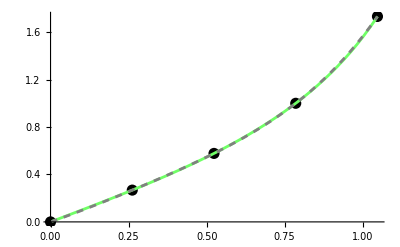

```mathematica
Исходные точки и полученный интерполяционный многочлен;
Gr1 = ListPlot[Tbl, PlotStyle -> {Black, PointSize[0.02]}];
Gr2 = Plot[f[x], {x, Subscript[x, 0], Subscript[x, n]}, PlotStyle -> RGBColor[0.44, 1, 0.4]];
Gr3 = Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]}, PlotStyle -> {Gray, Dashed}];
Show[Gr1, Gr2, Gr3]
```

```mathematica
Приближенное значение;
xx = Pi/9;
P[xx] // N
A = N[Abs[f[xx] - P[xx]], 2]
B = N[(A/(Abs[P[xx]]))*100, 2]
Print["Ответ: приближенное значение ", P[xx] // N, "; абсолютная погрешность ", A, "; относительная погрешность ", B, "%."]
```

Ответ: приближенное значение 0.36549; абсолютная погрешность 0.0015; относительная погрешность 0.42%.

0.36549

0.0015

0.42

{Cell[BoxData[TemplateBox[{"Ответ: приближенное значение ",0.3654903585579401`,"; абсолютная погрешность ",0.0015201242917363681`2.,"; относительная погрешность ",0.4159136502900097614`2.,"%."},RowDefault]],Print]}